√(x0^2+v0^2/ω^2)

k

m

-ArcTan[v0/(x0 ω)]

(k sqrt)/m

0≤t≤10

0.785398

5 m

2 N/m

1.75 kg

1.06904 √N/(√kg √m)

{A→5. m,0.785398→0.785398,ω→1.06904 √N/(√kg √m)}

5.

2.

1.75

1.06904

{A→5.,0.785398→0.785398,ω→1.06904}

-Graphics-

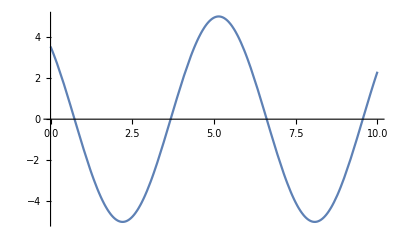

-Graphics-

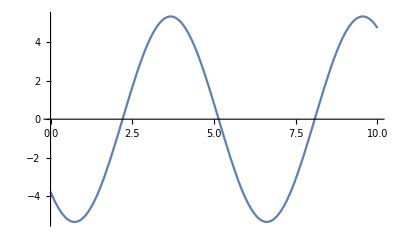

0.25 m

1.25 m/s

0.25

1.25

{x0→0.25 m,v0→1.25,ω→1.06904 √N/(√kg √m)}

{x0→0.25,v0→0.25,ω→1.06904}

√(x0^2+v0^2/ω^2)

-ArcTan[v0/(x0 ω)]

Quantity::compat: (Kilograms Meters)/Newtons and Meters^2 are incompatible units

√(0.0625 m^2+1.36719 kg m/N)

0.342327

-ArcTan[4.67707 √kg/(√m √N)]

-0.75204

{√(x0^2+v0^2/ω^2)→√(0.0625 m^2+1.36719 kg m/N),-ArcTan[v0/(x0 ω)]→-1. ArcTan[4.67707 √kg/(√m √N)],ω→1.06904 √N/(√kg √m)}

{√(x0^2+v0^2/ω^2)→0.342327,-ArcTan[v0/(x0 ω)]→-0.75204,ω→1.06904}

-Graphics-

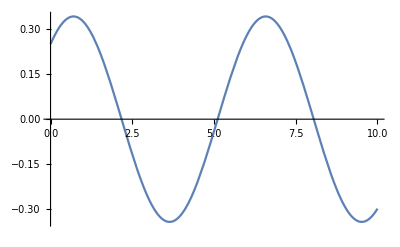

-Graphics-

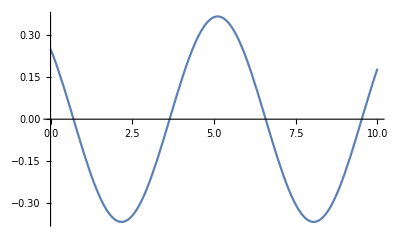

```mathematica
(*Exercício 01*)
(*Defining Variables and Functions*)
A
k
m
ϕ
ω=sqrt(k/m)
Clear[A, k, m, ϕ, ω]
(*Função Posição*)
x[t_]:=A*Cos[(ω*t+ϕ)]
(*Função Velocidade*)
v[t_]:=-ω*A*Sin[(ω*t+ϕ)]

(*Exercício 02*)
(*Setting Variables and Graph Plot*)
0≤ t≤10 
ϕ = N[Pi/4]
A21 = Quantity[5, "Meters"]
k21 = Quantity[2, ("Newtons")/("Meters")]
m21 = Quantity[1.75, "Kilograms"]
ω1 = N[((k21/m21)^(1/2))]
subs21 = {A -> N[A21], ϕ -> N[ϕ]  , ω -> N[ω1]}  

A22 = N[5]
k22 = N[2]
m22 = N[1.75]
ω2 = N[((k22/m22)^(1/2))]
subs22 = {A -> N[A22], ϕ -> N[ϕ]  , ω -> N[ω2]}  
Plot[x[t]/.subs21, {t, 0, 10}]
Plot[x[t]/.subs22, {t, 0, 10}]
Plot[v[t]/.subs21, {t, 0, 10}]
Plot[v[t]/.subs22, {t, 0, 10}]

(*Exercício 03*)
(*Setting Variables and Graph Plot*)
x01 = Quantity[0.25, "Meters"]
v01 = Quantity[1.25, ("Meters")/("Seconds")]
x02 = N[0.25]
v01 = N[1.25]
subsAϕ1 = {x0 -> x01, v0 -> v01, ω -> N[ω1]}
subsAϕ2 = {x0 -> x02, v0 -> v02, ω -> N[ω2]}
A = ((((x0)^2) +(((v0)^2)/((ω )^(2))))^(1/2))
ϕ = ArcTan[((-v0)/((ω)*(x0)))]
A31 = A/.subsAϕ1
A32 = A/.subsAϕ2
ϕ31 = ϕ/.subsAϕ1
ϕ32 = ϕ/.subsAϕ2
subs31 = {A -> N[A31], ϕ -> N[ϕ31]  , ω -> N[ω1]}  
subs32 = {A -> N[A32], ϕ -> N[ϕ32]  , ω -> N[ω2]}  
Plot[x[t]/.subs31, {t, 0, 10}]
Plot[x[t]/.subs32, {t, 0, 10}]
Plot[v[t]/.subs31, {t, 0, 10}]
Plot[v[t]/.subs32, {t, 0, 10}]
```